```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]


GenerateA[N1_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,A[[i,j]]=-ⅈ*Subscript[ω, i],
If[i<j,A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, b,i,j]],
A[[i,j]]=-Subscript[g, j,i]*Exp[ⅈ*Subscript[ϕ, b,j,i]]
];
];
]
];
A
]


GenerateB[N1_,m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,If[m!={}&& IntersectingQ[{i},m],A[[i,j]]=Subscript[ω, i]*Exp[-ⅈ*Subscript[ϕ, s,i]],A[[i,j]]=Subscript[ξ, i]*Exp[-ⅈ*Subscript[ϕ, s,i]]]];
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]],A[[i,j]]=Subscript[χ, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]],A[[i,j]]=Subscript[χ, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]]]];
];
];
A
]

BQH[N1_,m_]:=Module[{A,B,m1,m2,assump},
A=GenerateA[N1];
B=GenerateB[N1,m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=hui∈Reals;
For[i=1,i<=N1,i++,
assump=assump&&Subscript[ω, i]∈Reals&&Subscript[ξ, i]∈Reals&&Subscript[ϕ, s,i]∈Reals;
For[j=i,j<=N1,j++,
If[i!= j,assump=assump&&Subscript[g, i,j]∈Reals&&Subscript[χ, i,j]∈Reals&&Subscript[ϕ, t,i,j]∈Reals&&Subscript[ϕ, b,i,j]∈Reals;]
]];
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

ZeroPhase[Nmodes_]:=Module[{i,j,phases},
phases={};
For[i=1,i<=Nmodes,i++,
phases=phases~Join~{Subscript[ϕ, s,i]->0};
For[j=i,j<=Nmodes,j++,
If[i!= j,phases=phases~Join~{Subscript[ϕ, t,i,j]->0,Subscript[ϕ, b,i,j]->0};]
]];
phases
]

killSPDC[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],(*kill all g_{i,j}*)Flatten@Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}],(*kill all chi except pairwise (2j-1,2j)*)Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

killSPDCBS[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

SPDCBS2[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

(* with a phase *)
SPDCBS3[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->I g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->-I χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];


killomega[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}]];
killxi[N1_]:=Join[Table[Subscript[ξ,i]->0,{i,1,N1}]];
killg[N1_]:=Flatten[Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}]];
killchi[N1_]:=Flatten[Table[Subscript[χ,i,j]->0,{i,1,N1},{j,i+1,N1}]];


CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhoton[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonAnal[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/4 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(4 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+2 d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]


QFIperPhotonBQH[Nmodes_,EOM_]:=Module[{DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


FnNormal[Nmodes_,g_,χ_,t_]:=Module[{},
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{k,1,Nmodes},{h,1,Nmodes}];
y=Table[((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{h,1,Nmodes},{k,1,Nmodes}];
tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//N;

nout=1/4 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes/2//N;

Fcov=-1/2 tr-Nmodes;
Fcov/nout
]
```

```mathematica
Clear[g,χ]
Nmodes=2;
{Fcov2,Fdisp2,n2}=QFIperPhoton[Nmodes,χ,χ]
QFIperPhotonAnal[Nmodes,χ,χ]
LeadingOrderCheck[Fcov2,Fdisp2,n2,Nmodes]
```

{16 (t^2 χ^2+t^4 χ^4),2 (p1^2+p2^2+x1^2+x2^2+8 t (-p1 p2+x1 x2) χ+4 t^2 (3 p1^2+p2^2+x1^2+3 x2^2) χ^2+16 t^3 (-p1 p2+x1 x2) χ^3+16 t^4 (p1^2+x2^2) χ^4),1/2 (p1^2+p2^2+x1^2+x2^2+4 t (-p1 p2+x1 x2) χ+4 t^2 (1+p1^2+x2^2) χ^2)}

{16 (t^2 χ^2+t^4 χ^4),2 (p1^2+p2^2+x1^2+x2^2+8 t (-p1 p2+x1 x2) χ+4 t^2 (3 p1^2+p2^2+x1^2+3 x2^2) χ^2+16 t^3 (-p1 p2+x1 x2) χ^3+16 t^4 (p1^2+x2^2) χ^4),1/2 (p1^2+p2^2+x1^2+x2^2+4 t (-p1 p2+x1 x2) χ+4 t^2 (1+p1^2+x2^2) χ^2)}

leading order covariant 16 χ^4

True

leading order displacement 32 (p1^2+x2^2) χ^4

True

leading order mean photon number  2 (1+p1^2+x2^2) χ^2

True

```mathematica
Clear[g,χ]
Nmodes=3;
{Fcov3,Fdisp3,n3}=QFIperPhoton[Nmodes,χ,χ]
QFIperPhotonAnal[Nmodes,χ,χ]
LeadingOrderCheck[Fcov3,Fdisp3,n3,Nmodes]
```

{16 (2+t^2 χ^2) (t χ+t^3 χ^3)^2,2 (p2^2+p3^2+x1^2+x2^2+x3^2+p1^2 (1+6 t^2 χ^2+4 t^4 χ^4)^2-8 p1 t χ (1+t^2 χ^2) (-2 p3 t χ (1+t^2 χ^2)+p2 (1+6 t^2 χ^2+4 t^4 χ^4))+4 t χ (1+t^2 χ^2) (p3^2 t χ-2 p2 (p3+2 p3 t^2 χ^2)+4 p2^2 (t χ+t^3 χ^3)+(x1+x3+2 t x2 χ+2 t^2 x3 χ^2) (t (x1+3 x3) χ+2 (x2+t^2 x2 χ^2+t^3 x3 χ^3)))),1/2 (p1^2+p2^2+p3^2+x1^2+x2^2+x3^2+4 t (-p2 (p1+p3)+x2 (x1+x3)) χ+4 t^2 (2+p2^2+p1 (p1+p3)+x2^2+x3 (x1+x3)) χ^2+8 t^3 (-p1 p2+x2 x3) χ^3+4 t^4 (1+p1^2+x3^2) χ^4)}

{16 (2+t^2 χ^2) (t χ+t^3 χ^3)^2,2 (p2^2+p3^2+x1^2+x2^2+x3^2+p1^2 (1+6 t^2 χ^2+4 t^4 χ^4)^2-8 p1 t χ (1+t^2 χ^2) (-2 p3 t χ (1+t^2 χ^2)+p2 (1+6 t^2 χ^2+4 t^4 χ^4))+4 t χ (1+t^2 χ^2) (p3^2 t χ-2 p2 (p3+2 p3 t^2 χ^2)+4 p2^2 (t χ+t^3 χ^3)+(x1+x3+2 t x2 χ+2 t^2 x3 χ^2) (t (x1+3 x3) χ+2 (x2+t^2 x2 χ^2+t^3 x3 χ^3)))),1/2 (p1^2+p2^2+p3^2+x1^2+x2^2+x3^2+4 t (-p2 (p1+p3)+x2 (x1+x3)) χ+4 t^2 (2+p2^2+p1 (p1+p3)+x2^2+x3 (x1+x3)) χ^2+8 t^3 (-p1 p2+x2 x3) χ^3+4 t^4 (1+p1^2+x3^2) χ^4)}

leading order covariant 16 χ^8

True

leading order displacement 32 (p1^2+x3^2) χ^8

True

leading order mean photon number  2 (1+p1^2+x3^2) χ^4

True

```mathematica
Clear[g,χ]
Nmodes=4;
{Fcov4,Fdisp4,n4}=QFIperPhotonAnal[Nmodes,χ,χ]
LeadingOrderCheck[Fcov4,Fdisp4,n4,Nmodes]
```

{48 t^2 χ^2+16/81 t^4 χ^4 (729+900 t^2 χ^2+522 t^4 χ^4+144 t^6 χ^6+16 t^8 χ^8),2/81 (81 (p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2)-648 t (p1 p2+p3 (p2+p4)-x1 x2-x3 (x2+x4)) χ+324 t^2 (3 p1^2+4 p1 p3+4 p3^2+(2 p2+p4)^2+4 x2^2+(x1+2 x3)^2+4 x2 x4+3 x4^2) χ^2-216 t^3 (21 p1 p2+24 p2 p3+8 p1 p4+9 p3 p4-9 x1 x2-24 x2 x3-8 x1 x4-21 x3 x4) χ^3+108 t^4 (45 p2^2+3 (p1+p3) (11 p1+9 p3)+28 p2 p4+3 p4^2+3 x1^2+28 x1 x3+45 x3^2+3 (x2+x4) (9 x2+11 x4)) χ^4-432 t^5 (4 p3 (5 p2+p4)+p1 (26 p2+7 p4)-4 x2 (x1+5 x3)-(7 x1+26 x3) x4) χ^5+144 t^6 (42 p2^2+3 (p1+p3) (14 p1+5 p3)+15 p2 p4+p4^2+x1^2+15 x1 x3+42 x3^2+3 (x2+x4) (5 x2+14 x4)) χ^6-576 t^7 (19 p1 p2+9 p2 p3+3 p1 p4+p3 p4-x1 x2-9 x2 x3-3 x1 x4-19 x3 x4) χ^7+144 t^8 (33 p1^2+21 p2^2+28 p1 p3+4 p3^2+4 p2 p4+4 x2^2+4 x1 x3+21 x3^2+28 x2 x4+33 x4^2) χ^8-384 t^9 (3 p2 (4 p1+p3)+p1 p4-x1 x4-3 x3 (x2+4 x4)) χ^9+192 t^10 (9 p1^2+4 p1 p3+3 (p2^2+x3^2)+4 x2 x4+9 x4^2) χ^10+768 t^11 (-p1 p2+x3 x4) χ^11+256 t^12 (p1^2+x4^2) χ^12),1/2 (p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2)-2 t (p1 p2+p3 (p2+p4)-x1 x2-x3 (x2+x4)) χ+2 t^2 (3+p1^2+p1 p3+p3^2+p2 (p2+p4)+x2^2+x3 (x1+x3)+x2 x4+x4^2) χ^2-4/3 t^3 (3 p2 (p1+p3)+p1 p4-x1 x4-3 x3 (x2+x4)) χ^3+2/3 t^4 (3 p1^2+4 p1 p3+3 (2+p2^2+x3^2)+4 x2 x4+3 x4^2) χ^4+8/3 t^5 (-p1 p2+x3 x4) χ^5+8/9 t^6 (1+p1^2+x4^2) χ^6}

leading order covariant (256 χ^12)/81

True

leading order displacement 512/81 (p1^2+x4^2) χ^12

True

leading order mean photon number  8/9 (1+p1^2+x4^2) χ^6

True

```mathematica
(* single mode *)
Nmodes=1;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
{F1,Fd1,n1}=QFIperPhotonBQH[Nmodes,EOM]/.{x1->0,p1->0,Subscript[ω, 1]->0}//FullSimplify
F1/n1//FullSimplify

Subscript[ω, 1]=0;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Scovar//MatrixForm
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
Σin//MatrixForm
Σin//Eigenvectors
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
G//Eigenvectors
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;

Tr[Inverse[Σin].G.Σin.G]//FullSimplify
Gt=Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes];
Tr[Inverse[S.Transpose[S]].Gt.S.Transpose[S].Gt]//FullSimplify
```

{-1+Cosh[4 t ξ1],0,Sinh[t ξ1]^2}

8 Cosh[t ξ1]^2

(ⅇ^(t ξ1) | 0
0 | ⅇ^(-t ξ1))

(ⅇ^(2 t ξ1) | 0
0 | ⅇ^(-2 t ξ1))

{{0,1},{1,0}}

{{-ⅈ,1},{ⅈ,1}}

-2 Cosh[4 t ξ1]

-2 Cosh[4 t ξ1]

```mathematica
QT[2]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{-ⅈ/(√2),0,ⅈ/(√2),0},{0,-ⅈ/(√2),0,ⅈ/(√2)}}

```mathematica
Nmodes=2;
G=Transpose[CovarBasis[Nmodes]].ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]].{{h11,h12,h13,h14},{h21,h22,h23,h24},{h31,h32,h33,h34},{h41,h42,h43,h44}}.CovarBasis[Nmodes]
ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]].{{h11,h12,h13,h14},{h21,h22,h23,h24},{h31,h32,h33,h34},{h41,h42,h43,h44}}
```

{{h21,h23,h22,h24},{h41,h43,h42,h44},{-h11,-h13,-h12,-h14},{-h31,-h33,-h32,-h34}}

{{h21,h22,h23,h24},{-h11,-h12,-h13,-h14},{h41,h42,h43,h44},{-h31,-h32,-h33,-h34}}

```mathematica
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},1]].{{h11,h12},{h12*,h22}}
```

{{Conjugate[h12],h22},{-h11,-h12}}

```mathematica
Σ=S.Transpose[S];
eig=Eigensystem[Σ]
U=Transpose[eig[[2]]];
Σ==U.DiagonalMatrix[eig[[1]]].Inverse[U]
Tr[Inverse[Σ].Gt.Σ.Gt]//FullSimplify

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Gt=Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes];

Gp=Inverse[U].Gt.U;
Opt=Inverse[U].ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},1]].{{h11,h12},{h12*,h22}}.U
Tr[DiagonalMatrix[1/eig[[1]]].Gp.DiagonalMatrix[eig[[1]]].Gp]//FullSimplify


Sum[eig[[1,k]]/eig[[1,i]] Gp[[i,k]]Gp[[k,i]],{i,1,2},{k,1,2}]//FullSimplify
Sum[eig[[1,k]]/eig[[1,i]] Subscript[M, i,k] Subscript[M, k,i],{i,1,2},{k,1,2}]//FullSimplify
Tr[DiagonalMatrix[1/eig[[1]]].Opt.DiagonalMatrix[eig[[1]]].Opt]//FullSimplify
Sum[eig[[1,k]] ,{k,1,2}]//FullSimplify

U.{{M11,M12},{M21,M22}}.Inverse[U]
Gt
G
```

{{ⅇ^(-2 t ξ1),ⅇ^(2 t ξ1)},{{0,1},{1,0}}}

True

-2 Cosh[4 t ξ1]

{{-h12,-h11},{h22,Conjugate[h12]}}

-2 Cosh[4 t ξ1]

-2 Cosh[4 t ξ1]

M_(1,1)^2+2 Cosh[4 t ξ1] M_(1,2) M_(2,1)+M_(2,2)^2

h12^2+Conjugate[h12]^2-2 h11 h22 Cosh[4 t ξ1]

2 Cosh[2 t ξ1]

{{M22,M21},{M12,M11}}

{{0,1},{-1,0}}

{{0,1},{-1,0}}

```mathematica
(*PARAMETERS*)nMax=200;          (*Fock cutoff*)
r=1;         (*squeezing parameter*)

(*BASIS:Fock states|n>*)
basis=IdentityMatrix[nMax+1];

(*Annihilation and creation operators*)
a=SparseArray[Table[If[m==n-1,Sqrt[n],0],{m,0,nMax},{n,0,nMax}]];
adag=Transpose[a];

(*Quadratures*)
X=(a+adag)/Sqrt[2];
P=(a-adag)/(I Sqrt[2]);

(*Quadratic generators (example)*)
K1=1/2 (X.X-P.P);       (*squeezing along X*)
K2=1/2 (X.P+P.X);       (*45-degree squeezing*)

Glist={X,P,K1,K2};         (*choose your basis*)

(*Single-mode squeezed vacuum|psi> =S(r)|0>*)

(*Squeezing operator S(r) in Fock basis:use standard series;here,directly from definition on|0>*)
squeezedVacuum[r_,nmax_]:=Module[{psi,norm,k},psi=ConstantArray[0.,nmax+1];
norm=1/Sqrt[Cosh[r]];
For[k=0,k<=Floor[nmax/2],k++,psi[[2 k+1]]=norm*((-Tanh[r])^k)*Sqrt[Factorial[2 k]]/(2^k Factorial[k]);];
psi/Sqrt[psi.Conjugate[psi]]];

psi=squeezedVacuum[r,nMax];
rho=Outer[Times,psi,Conjugate[psi]];  (* |psi><psi|*)

(*EXPECTATION VALUES*)
expect[rho_,A_]:=Tr[rho.A];

(*QFIM via Reilly et al.Eq.(4):F_{μν}=2<{G_μ,G_ν}>-4<G_μ><G_ν> =4 Cov(G_μ,G_ν)*)

qfim[rho_,Gs_List]:=Module[{m=Length[Gs],F,mu,nu,Gmu,Gnu,anticomm,eAC,eMu,eNu},F=ConstantArray[0.,{m,m}];
For[mu=1,mu<=m,mu++,Gmu=Gs[[mu]];
eMu=Chop[expect[rho,Gmu]];
For[nu=1,nu<=m,nu++,Gnu=Gs[[nu]];
eNu=Chop[expect[rho,Gnu]];
anticomm=Gmu.Gnu+Gnu.Gmu;
eAC=Chop[expect[rho,anticomm]]/2;
F[[mu,nu]]=2 eAC-4 eMu eNu;];];
F];

F=qfim[rho,Glist]//N;
F//MatrixForm

(*Diagonalize to get optimal generator coefficients*)
valsVecs=Eigensystem[F];
lambdaMax=Max[valsVecs[[1]]];
optVec=valsVecs[[2,First@Ordering[valsVecs[[1]],-1]]];

lambdaMax
optVec
```

(0.135335 | 0. | 0. | 0.
0. | 7.38906 | 0. | 0.
0. | 0. | 7.57706 | 0.
0. | 0. | 0. | 1.)

7.57706

{0.,0.,1.,0.}

```mathematica
(*1. Symplectic structure and squeezed state*)Ω={{0,1},{-1,0}};   (*symplectic form for (X,P)*)

V[r_]:=1/2 {{Exp[-2 r],0},{0,Exp[2 r]}};  (*cov.matrix of S(r)|0>*)
d={0,0};                                    (*no displacement*)

(*2. Choose Gaussian generator set via symplectic generators K_μ*)

Kφ={{0,1},{-1,0}};
Kx={{1,0},{0,-1}};
K45={{0,1},{1,0}};

Klist={Kφ,Kx,K45};


Klist={Kφ,Ks};         (*extend this list as needed*)

(*3. QFIM for pure,centered Gaussian state in terms of V and K_μ*)

qfimGaussian[Vmat_,Ωmat_,Klist_List]:=Module[{m=Length[Klist],F,mu,nu,Aμ,Aν},F=ConstantArray[0.,{m,m}];
For[mu=1,mu<=m,mu++,Aμ=Vmat.Ωmat.Klist[[mu]];
For[nu=1,nu<=m,nu++,Aν=Vmat.Ωmat.Klist[[nu]];
F[[mu,nu]]=2*Tr[Aμ.Aν];  (*F_{μν}=2 Tr[(V Ω K_μ)(V Ω K_ν)]*)];];
(F+Transpose[F])/2  (*enforce symmetry*)];

(*4. Build QFIM at chosen squeezing r and diagonalize*)

rval=0.8;
Vnow=V[rval];

Fgauss=qfimGaussian[Vnow,Ω,Klist]//N;
Fgauss//MatrixForm

{vals,vecs}=Eigensystem[Fgauss];
λmax=Max[vals];
optVec=vecs[[First@Ordering[vals,-1]]];   (*coefficients O_μ*)

λmax
optVec
```

(12.2866 | 0.
0. | 1.)

12.2866

{-1.,0.}

```mathematica
(*Symplectic form for 2 modes*)
Ω2=ArrayFlatten[{{{0,1},{-1,0}},{{0,0},{0,0}}}];
Ω2=ArrayFlatten[{{{0,1},{-1,0}},{{0,1},{-1,0}}}];  (*better:block-diag of single-mode Ω*)

Ω1={{0,1},{-1,0}};
Ω2=ArrayFlatten[{{Ω1,0 Ω1},{0 Ω1,Ω1}}];

Vtmsv[r_]:=Module[{ch=Cosh[2 r],sh=Sinh[2 r],I2,Z},I2=IdentityMatrix[2];
Z=DiagonalMatrix[{1,-1}];
1/2 ArrayFlatten[{{ch I2,sh Z},{sh Z,ch I2}}]];

d2={0,0,0,0};  (*no displacement*)

(*Local phase rotations:block-diagonal Js*)
J={{0,1},{-1,0}};

Kφ1=ArrayFlatten[{{J,0 J},{0 J,0 J}}];   (*acts on mode 1 only*)
Kφ2=ArrayFlatten[{{0 J,0 J},{0 J,J}}];   (*acts on mode 2 only*)

(*Two-mode squeezing:mixes X1,X2 and P1,P2 with opposite sign*)
Ktms=ArrayFlatten[{{{0,0},{1,0}},{{0,-1},{0,0}}}];
(*Better,define in 4x4 explicitly in (X1,P1,X2,P2) basis:*)
Ktms={{0,0,1,0},{0,0,0,-1},{1,0,0,0},{0,-1,0,0}};

Klist={Kφ1,Kφ2,Ktms};
labels={"Kφ1","Kφ2","Ktms"};

qfimGaussianPure[Vmat_,Ωmat_,Klist_List]:=Module[{m=Length[Klist],F,mu,nu,Bμ,Bν},F=ConstantArray[0.,{m,m}];
For[mu=1,mu<=m,mu++,Bμ=Transpose[Ωmat].Klist[[mu]].Vmat;
For[nu=1,nu<=m,nu++,Bν=Transpose[Ωmat].Klist[[nu]].Vmat;
F[[mu,nu]]=2*Tr[Bμ.Bν];];];
(F+Transpose[F])/2];


rval=20.0;
Vnow=Vtmsv[rval];

F2=qfimGaussianPure[Vnow,Ω2,Klist]//N;
F2//MatrixForm

{vals,vecs}=Eigensystem[F2];
λmax=Max[vals];
idx=First@Ordering[vals,-1];
optVec=vecs[[idx]];   (*coefficients for {Kφ1,Kφ2,Ktms}*)

λmax
Thread[labels->optVec]
```

(1.38516×10^34 | 1.38516×10^34 | 0.
1.38516×10^34 | 1.38516×10^34 | 0.
0. | 0. | 0.)

2.77031×10^34

{Kφ1→0.707107,Kφ2→0.707107,Ktms→0.}

```mathematica
Ω1={{0,1},{-1,0}};
Ω2=ArrayFlatten[{{Ω1,0 Ω1},{0 Ω1,Ω1}}];

Vtmsv[r_]:=Module[{ch=Cosh[2 r],sh=Sinh[2 r],I2,Z},I2=IdentityMatrix[2];
Z=DiagonalMatrix[{1,-1}];
1/2 ArrayFlatten[{{ch I2,sh Z},{sh Z,ch I2}}]];

d2={0,0,0,0};

J={{0,1},{-1,0}};
Kφ1=ArrayFlatten[{{J,0 J},{0 J,0 J}}];
Kφ2=ArrayFlatten[{{0 J,0 J},{0 J,J}}];
Ktms={{0,0,1,0},{0,0,0,-1},{1,0,0,0},{0,-1,0,0}};
Kbs={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
Klist={Kφ1,Kφ2,Ktms,Kbs};
labels={"Kφ1","Kφ2","Ktms","Kbs"};
qfimGaussianPure[Vmat_,Ωmat_,Klist_List]:=Module[{m=Length[Klist],F,mu,nu,Bμ,Bν},F=ConstantArray[0.,{m,m}];
For[mu=1,mu<=m,mu++,Bμ=Transpose[Ωmat].Klist[[mu]].Vmat;
For[nu=1,nu<=m,nu++,Bν=Transpose[Ωmat].Klist[[nu]].Vmat;
F[[mu,nu]]=2*Tr[Bμ.Bν];];];
(F+Transpose[F])/2];
rval=10.0;
Vnow=Vtmsv[rval];

F2=qfimGaussianPure[Vnow,Ω2,Klist]//N;
F2//MatrixForm

{vals,vecs}=Eigensystem[F2];
λmax=Max[vals];
idx=First@Ordering[vals,-1];
optVec=vecs[[idx]];   (*{Oφ1,Oφ2,Otms,Obs}*)

λmax
Thread[labels->optVec]
```

(5.88463×10^16 | 5.88463×10^16 | 0. | 0.
5.88463×10^16 | 5.88463×10^16 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 2.35385×10^17)

2.35385×10^17

{Kφ1→0.,Kφ2→0.,Ktms→0.,Kbs→1.}

```mathematica
Nmodes=2;
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}]
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;

Tr[Inverse[Σin].G.Σin.G]//FullSimplify
Gt=Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes];
Tr[Inverse[S.Transpose[S]].Gt.S.Transpose[S].Gt]//FullSimplify
```

{{0,g,0,χ},{-g,0,χ,0},{0,χ,0,g},{χ,0,-g,0}}

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

```mathematica
Σ=S.Transpose[S];
eig=Eigensystem[Σ];
U=Transpose[eig[[2]]];
Tr[Inverse[Σ].Gt.Σ.Gt]//FullSimplify

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Gt=Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes];


Gp=Inverse[U].Gt.U;

"Sum"
Tr[DiagonalMatrix[1/eig[[1]]].Gp.DiagonalMatrix[eig[[1]]].Gp]//FullSimplify


Sum[eig[[1,k]]/eig[[1,i]] Gp[[i,k]]Gp[[k,i]],{i,1,2 Nmodes},{k,1,2 Nmodes}]//FullSimplify
Sum[eig[[1,k]]/eig[[1,i]] Subscript[M, i,k] Subscript[M, k,i],{i,1,2 Nmodes},{k,1,2 Nmodes}]//FullSimplify
Sum[eig[[1,k]] ,{k,1,2 Nmodes}]//FullSimplify

(*U.{{M11,M12},{M21,M22}}.Inverse[U]
Gt
G
```

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

Sum

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

1/((g^2-χ^2)^2)((g^2-χ^2)^2 M_(1,1)^2+2 (g^2-χ^2)^2 M_(1,2) M_(2,1)+g^4 M_(2,2)^2-2 g^2 χ^2 M_(2,2)^2+χ^4 M_(2,2)^2+2 g^4 M_(1,3) M_(3,1)+4 g^2 χ^2 M_(1,3) M_(3,1)+2 g^4 M_(2,3) M_(3,2)+4 g^2 χ^2 M_(2,3) M_(3,2)+g^4 M_(3,3)^2-2 g^2 χ^2 M_(3,3)^2+χ^4 M_(3,3)^2+2 g^4 M_(1,4) M_(4,1)+4 g^2 χ^2 M_(1,4) M_(4,1)+2 g^4 M_(2,4) M_(4,2)+4 g^2 χ^2 M_(2,4) M_(4,2)-8 g^2 χ^2 Cosh[2 t √(-g^2+χ^2)] (M_(1,3) M_(3,1)+M_(2,3) M_(3,2)+M_(1,4) M_(4,1)+M_(2,4) M_(4,2))+2 χ^4 Cosh[4 t √(-g^2+χ^2)] (M_(1,3) M_(3,1)+M_(2,3) M_(3,2)+M_(1,4) M_(4,1)+M_(2,4) M_(4,2))+2 g^4 M_(3,4) M_(4,3)-4 g^2 χ^2 M_(3,4) M_(4,3)+2 χ^4 M_(3,4) M_(4,3)+(g^2-χ^2)^2 M_(4,4)^2)

(4 (g^2-χ^2 Cosh[2 t √(-g^2+χ^2)]))/(g^2-χ^2)

{{0,0,ξ1,0},{0,0,0,ξ2},{ξ1,0,0,0},{0,ξ2,0,0}}

{4 Sinh[2 t ξ1]^2,0,2 Sinh[t ξ1]^2}

8 Cosh[t ξ1]^2

{-2+Cosh[4 t ξ1]+Cosh[4 t ξ2],0,1/2 (-2+Cosh[2 t ξ1]+Cosh[2 t ξ2])}

(2 (-2+Cosh[4 t ξ1]+Cosh[4 t ξ2]))/(-2+Cosh[2 t ξ1]+Cosh[2 t ξ2])

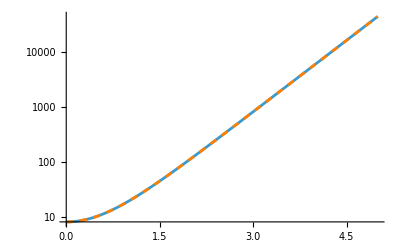

```mathematica
Clear[pl1,pl2]
Subscript[ξ,1]=ξ1;
Subscript[ξ,2]=ξ2;
Nmodes=2;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killomega[Nmodes]/.killg[Nmodes]/.killchi[Nmodes]
{F2,Fd2,n2}=QFIperPhotonBQH[Nmodes,EOM]/.{x1->0,p1->0,x2->0,p2->0}/.ξ2->ξ1//FullSimplify
F2/n2//FullSimplify
pl1=LogPlot[F2/n2/.{ξ1->1},{t,0,5}];

{F22,Fd22,n22}=QFIperPhotonBQH[Nmodes,EOM]/.{x1->0,p1->0,x2->0,p2->0}//FullSimplify
F22/n22//FullSimplify
pl2=LogPlot[F22/n22/.{ξ1->1,ξ2->1},{t,0,5},PlotStyle->{Orange,Dashed}];


Show[pl1,pl2]
```

```mathematica
Nmodes=3;
Subscript[ξ,1]=ξ1;
Subscript[ξ,2]=ξ2;
Subscript[ξ,3]=ξ3;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killomega[Nmodes]/.killg[Nmodes]/.killchi[Nmodes]
QFIperPhotonBQH[Nmodes,EOM]/.{x1->0,p1->0,x2->0,x3->0,p2->0,p3->0}/.ξ2->ξ1/.ξ3->ξ1//FullSimplify

QFIperPhotonBQH[Nmodes,EOM]/.{x1->0,p1->0,x2->0,x3->0,p2->0,p3->0}//FullSimplify
```

{{0,0,0,ξ1,0,0},{0,0,0,0,ξ2,0},{0,0,0,0,0,ξ3},{ξ1,0,0,0,0,0},{0,ξ2,0,0,0,0},{0,0,ξ3,0,0,0}}

{6 Sinh[2 t ξ1]^2,0,3 Sinh[t ξ1]^2}

{-3+Cosh[4 t ξ1]+Cosh[4 t ξ2]+Cosh[4 t ξ3],0,1/2 (-3+Cosh[2 t ξ1]+Cosh[2 t ξ2]+Cosh[2 t ξ3])}

{-1+Cosh[4 t ξ1],2 ⅇ^(-4 t ξ1) (p1^2+ⅇ^(8 t ξ1) x1^2),1/2 (-1+(1+p1^2+x1^2) Cosh[2 t ξ1]+(-p1^2+x1^2) Sinh[2 t ξ1])}

(8 ⅇ^(-2 t ξ1) (p1^2+ⅇ^(8 t ξ1) x1^2))/(1-2 ⅇ^(2 t ξ1)+2 p1^2+ⅇ^(4 t ξ1) (1+2 x1^2))

1/2 (-1+(1+p1^2+x1^2) Cosh[2 t ξ1]+(-p1^2+x1^2) Sinh[2 t ξ1])

{(4 Sinh[2 t ξ1]^2)/(-1+(1+x1^2) Cosh[2 t ξ1]+x1^2 Sinh[2 t ξ1]),(4 ⅇ^(4 t ξ1) x1^2)/(-1+(1+x1^2) Cosh[2 t ξ1]+x1^2 Sinh[2 t ξ1])}

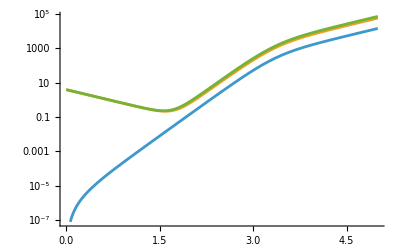

```mathematica
(* add displacement *)
Clear[x1,x2,x3,x4,p1,p2,p3,p4]
Nmodes=1;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
{F1,Fd1,n1}=QFIperPhotonBQH[Nmodes,EOM]/.{Subscript[ω, 1]->0}//FullSimplify
Fd1/n1//Simplify
n1//FullSimplify
Evaluate[{F1/n1,Fd1/n1}/.{p1->0}]//FullSimplify
LogPlot[Evaluate[{F1/n1,Fd1/n1,(F1+Fd1)/n1}/.{ξ1->1,p1->1000,x1->1}],{t,0,5}]
```

```mathematica
2 Cosh[4 t]//Expand
```

2 Cosh[4 t]

{{0,0,ξ1,0},{0,0,0,ξ2},{ξ1,0,0,0},{0,ξ2,0,0}}

{-2+Cosh[4 t ξ1]+Cosh[4 t ξ2],2 (ⅇ^(-4 t ξ1) p1^2+ⅇ^(-4 t ξ2) p2^2+ⅇ^(4 t ξ1) x1^2+ⅇ^(4 t ξ2) x2^2),1/4 (-4+ⅇ^(-2 t ξ1) (1+2 p1^2)+ⅇ^(-2 t ξ2) (1+2 p2^2)+ⅇ^(2 t ξ1) (1+2 x1^2)+ⅇ^(2 t ξ2) (1+2 x2^2))}

Coherent and displacement contribution

{4 Sinh[2 t ξ]^2,4 ⅇ^(4 t ξ) x^2,-1+(1+x^2) Cosh[2 t ξ]+x^2 Sinh[2 t ξ]}

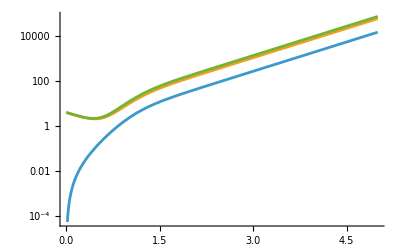

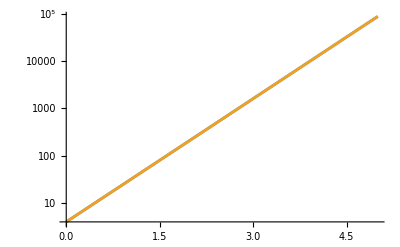

```mathematica
Nmodes=2;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killomega[Nmodes]/.killg[Nmodes]/.killchi[Nmodes]


{F2,Fd2,n2}=QFIperPhotonBQH[Nmodes,EOM]//FullSimplify

"Coherent and displacement contribution"
Evaluate[{F2,Fd2,n2}/.{p1->0,p2->0,p3->0,x1->x,x2->x,x3->x,ξ1->ξ,ξ2->ξ,ξ3->ξ}]//FullSimplify

LogPlot[Evaluate[{F2/n2,Fd2/n2,(F2+Fd2)/n2}/.{ξ1->1,ξ2->1,p1->10,p2->10,x1->1,x2->1}],{t,0,5}]


LogPlot[Evaluate[{(F1+Fd1)/n1,(F2+Fd2)/n2}/.{ξ1->1,ξ2->1,p1->0,p2->0,x1->10,x2->10}],{t,0,5}]
```

```mathematica
Nmodes=3;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killomega[Nmodes]/.killg[Nmodes]/.killchi[Nmodes]
{F3,Fd3,n3}=QFIperPhotonBQH[Nmodes,EOM]//FullSimplify
"Coherent and displacement contribution"
Evaluate[{F3,Fd3,n3}/.{p1->0,p2->0,p3->0,x1->x,x2->x,x3->x,ξ1->ξ,ξ2->ξ,ξ3->ξ}]//FullSimplify
```

{{0,0,0,ξ1,0,0},{0,0,0,0,ξ2,0},{0,0,0,0,0,ξ3},{ξ1,0,0,0,0,0},{0,ξ2,0,0,0,0},{0,0,ξ3,0,0,0}}

{-3+Cosh[4 t ξ1]+Cosh[4 t ξ2]+Cosh[4 t ξ3],2 (ⅇ^(-4 t ξ1) p1^2+ⅇ^(-4 t ξ2) p2^2+ⅇ^(-4 t ξ3) p3^2+ⅇ^(4 t ξ1) x1^2+ⅇ^(4 t ξ2) x2^2+ⅇ^(4 t ξ3) x3^2),1/4 (-6+ⅇ^(-2 t ξ1) (1+2 p1^2)+ⅇ^(-2 t ξ2) (1+2 p2^2)+ⅇ^(-2 t ξ3) (1+2 p3^2)+ⅇ^(2 t ξ1) (1+2 x1^2)+ⅇ^(2 t ξ2) (1+2 x2^2)+ⅇ^(2 t ξ3) (1+2 x3^2))}

Coherent and displacement contribution

{6 Sinh[2 t ξ]^2,6 ⅇ^(4 t ξ) x^2,3/4 (-2+ⅇ^(-2 t ξ)+ⅇ^(2 t ξ) (1+2 x^2))}

One mode

{2 Sinh[2 t ξ1]^2,2 (p1^2+x1^2) Cosh[4 t Abs[ξ1]]-(2 (p1^2-x1^2) Abs[ξ1] Sinh[4 t Abs[ξ1]])/ξ1,1/(2 ξ1)(ξ1 (-1+(1+p1^2+x1^2) Cosh[2 t Abs[ξ1]])-(p1^2-x1^2) Abs[ξ1] Sinh[2 t Abs[ξ1]])}

Two modes

{{0,0,0,χ_(1,2)},{0,0,χ_(1,2),0},{0,χ_(1,2),0,0},{χ_(1,2),0,0,0}}

{4 Sinh[2 t χ_(1,2)]^2,2 (x1^2+x2^2) Cosh[4 t χ_(1,2)]+4 x1 x2 Sinh[4 t χ_(1,2)],-1+1/2 (2+x1^2+x2^2) Cosh[2 t χ_(1,2)]+x1 x2 Sinh[2 t χ_(1,2)]}

Four modes

{{0,0,0,0,0,χ,0,0},{0,0,0,0,χ,0,0,0},{0,0,0,0,0,0,0,χ},{0,0,0,0,0,0,χ,0},{0,χ,0,0,0,0,0,0},{χ,0,0,0,0,0,0,0},{0,0,0,χ,0,0,0,0},{0,0,χ,0,0,0,0,0}}

{8 Sinh[2 t χ]^2,2 (x1^2+x2^2+x3^2+x4^2) Cosh[4 t χ]+4 (x1 x2+x3 x4) Sinh[4 t χ],-2+1/2 (4+x1^2+x2^2+x3^2+x4^2) Cosh[2 t χ]+(x1 x2+x3 x4) Sinh[2 t χ]}

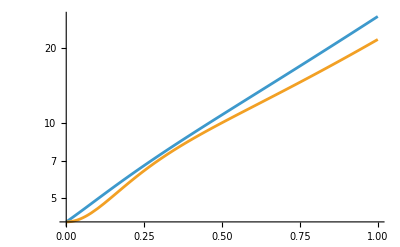

True

```mathematica
(* compare SMSV with TMSV*)
Nmodes=1;
"One mode"
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
{F1,Fd1,n1}=QFIperPhotonBQH[Nmodes,EOM]/.{Subscript[ω, 1]->0}//Simplify

"Two modes"
Nmodes=2;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killomega[Nmodes]/.killg[Nmodes]/.killxi[Nmodes]
{F2,Fd2,n2}=QFIperPhotonBQH[Nmodes,EOM]/.{p1->0,p2->0,p3->0}//Simplify

"Four modes"
Nmodes=4;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killSPDC[Nmodes]
{F4,Fd4,n4}=QFIperPhotonBQH[Nmodes,EOM]/.{p1->0,p2->0,p3->0,p4->0}//Simplify

LogPlot[{(F4+Fd4)/n4/.{χ->1,p1->0,p2->0,p3->0,p4->0,x1->1,x2->1,x3->1,x4->1},(F4+Fd4)/n4/.{χ->1,p1->0,p2->0,p3->0,p4->0,x1->1,x2->0,x3->0,x4->0}},{t,0,1}]

(*"Three modes"
Nmodes=3;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killomega[Nmodes]/.killg[Nmodes]/.killxi[Nmodes]/.{Subscript[χ, 1,2]->χ,Subscript[χ, 2,3]->χ,Subscript[χ, 1,3]->χ}

p1=0;p2=0;p3=0;x1=0;x2=0;x3=0;
{F3,Fd3,n3}=QFIperPhotonBQH[Nmodes,EOM]//FullSimplify
*)
```

```mathematica
(*add a BS *)
Clear[x1,x2,x3,p1,p2,p3]
Nmodes=1;
"One mode"
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
{F1,Fd1,n1}=QFIperPhotonBQH[Nmodes,EOM]/.{Subscript[ω, 1]->0}//Simplify

"Two modes"
Nmodes=2;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killSPDCBS[Nmodes]
{F2,Fd2,n2}=QFIperPhotonBQH[Nmodes,EOM]/.{p1->0,p2->0,p3->0}//Simplify
```

One mode

{2 Sinh[2 t ξ1]^2,2 (p1^2+x1^2) Cosh[4 t Abs[ξ1]]-(2 (p1^2-x1^2) Abs[ξ1] Sinh[4 t Abs[ξ1]])/ξ1,1/(2 ξ1)(ξ1 (-1+(1+p1^2+x1^2) Cosh[2 t Abs[ξ1]])-(p1^2-x1^2) Abs[ξ1] Sinh[2 t Abs[ξ1]])}

Two modes

{{0,g,0,χ},{-g,0,χ,0},{0,χ,0,g},{χ,0,-g,0}}

{(8 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2),1/((g^2-χ^2)^2)2 g (g^3 (x1^2+x2^2)+2 g^2 (-x1^2+x2^2) χ+2 g (x1^2+x2^2) χ^2+(-x1^2+x2^2) χ^3)-1/((g^2-χ^2)^2)4 g χ (g^2 (-x1^2+x2^2)+2 g (x1^2+x2^2) χ+(-x1^2+x2^2) χ^2) Cosh[2 t √(-g^2+χ^2)]+(2 χ^3 (g (-x1^2+x2^2)+(x1^2+x2^2) χ) Cosh[4 t √(-g^2+χ^2)])/((g^2-χ^2)^2)+(8 x1 x2 χ (-g^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[2 t √(-g^2+χ^2)])/((-g^2+χ^2)^(3/2)),1/(2 (g-χ) (g+χ))(g^2 (x1^2+x2^2)+g (-x1^2+x2^2) χ+2 χ^2-χ (g (-x1^2+x2^2)+(2+x1^2+x2^2) χ) Cosh[2 t √(-g^2+χ^2)]-2 x1 x2 χ √(-g^2+χ^2) Sinh[2 t √(-g^2+χ^2)])}

0

0

(2 χ^2 Sinh[t √(-g^2+χ^2)]^2)/(-g^2+χ^2)

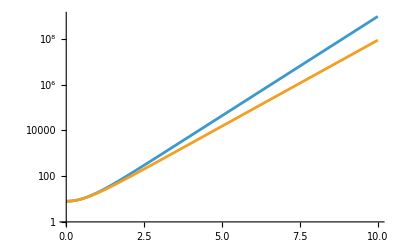

```mathematica
Fd2/.{p1->0,p2->0,x1->x,x2->x,g->0}//FullSimplify
Fd2/.{p1->0,p2->0,x1->x,x2->0}//FullSimplify
n2/.{p1->0,p2->0,x1->x,x2->0}//FullSimplify
LogPlot[{F2/n2/.{χ->1,g->0,p1->0,p2->0,x1->0,x2->0},F2/n2/.{χ->1,g->0.5,p1->0,p2->0,x1->0,x2->0}},{t,0,10}]
```

```mathematica
"Two modes vs four"
Nmodes=2;
x1=0;x2=0;x3=0;p1=0;p2=0;p3=0;p4=0;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killSPDCBS[Nmodes]
{F2,Fd2,n2}=QFIperPhotonBQH[Nmodes,EOM]//Simplify
F2/n2//Simplify

Nmodes=4;
x1=0;x2=0;x3=0;p1=0;p2=0;p3=0;p4=0;x4=0;p4=0;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.killSPDCBS[Nmodes]
EOM//MatrixForm
{F4,Fd4,n4}=QFIperPhotonBQH[Nmodes,EOM]//Simplify
F4/n4//Simplify
```

Two modes vs four

{{0,g,0,χ},{-g,0,χ,0},{0,χ,0,g},{χ,0,-g,0}}

{(8 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2),0,(2 χ^2 Sinh[t √(-g^2+χ^2)]^2)/(-g^2+χ^2)}

(8 g^2-4 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2)

{{0,g,0,0,0,χ,0,0},{-g,0,0,0,χ,0,0,0},{0,0,0,g,0,0,0,χ},{0,0,-g,0,0,0,χ,0},{0,χ,0,0,0,g,0,0},{χ,0,0,0,-g,0,0,0},{0,0,0,χ,0,0,0,g},{0,0,χ,0,0,0,-g,0}}

(0 | g | 0 | 0 | 0 | χ | 0 | 0
-g | 0 | 0 | 0 | χ | 0 | 0 | 0
0 | 0 | 0 | g | 0 | 0 | 0 | χ
0 | 0 | -g | 0 | 0 | 0 | χ | 0
0 | χ | 0 | 0 | 0 | g | 0 | 0
χ | 0 | 0 | 0 | -g | 0 | 0 | 0
0 | 0 | 0 | χ | 0 | 0 | 0 | g
0 | 0 | χ | 0 | 0 | 0 | -g | 0)

{(16 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2),0,(4 χ^2 Sinh[t √(-g^2+χ^2)]^2)/(-g^2+χ^2)}

(8 g^2-4 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2)

```mathematica
Flatten@Table[If[j==i+1&&OddQ[i],Subscript[g,i,j],0],{i,1,N1},{j,i+1,N1}]
```

Table::iterb: Iterator {i,1,N1} does not have appropriate bounds.

Table[If[j==i+1&&OddQ[i],g_(i,j),0],{i,1,N1},{j,i+1,N1}]

```mathematica
If[j==i+1&&OddQ[i],Print[{i,j}],{i,1,4},{j,i+1,4}]
```

{5,1,4}